```mathematica
f[t_]:=2Exp[0.7944t]
f[6]
```

234.991

```mathematica
First@FindRoot[420-100 E^k,{k,0}]
```

k→1.43508

```mathematica
Exp[1.435]
```

4.19965

```mathematica
area[t_]:= π r[t]^2 
area'[t]
r'[t_]:=1
r[t]:=30
```

60 π

```mathematica
Clear[r]
```

```mathematica
linearize[f_,a_]:=f[a]+f'[a](x-a)
linearize[f,2]
```

32+80 (-2+x)

```mathematica
linearize[f[x],2]//Expand//TraditionalForm
```

x f(x)'(2)-2 f(x)'(2)+f(x)(2)

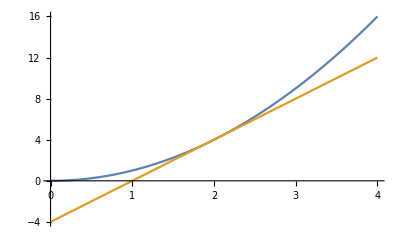

```mathematica
Plot[{x^2,4x-4},{x,0,4}]
```

80 x-128

32.08

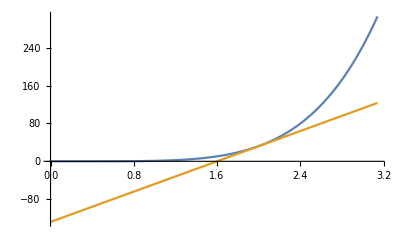

```mathematica
f[x_]:=x^5;
a=2;
linearized=linearize[f,a];
linearized//Expand//TraditionalForm
linearized/.x->2.001//N
Plot[{f[x],linearized},{x,0,π}]
```

```mathematica
Dt[x^-1,x]//Simplify
1/1000+(%/.x->1000)(2)
```

-1/x^2

```mathematica
499/500000//N
1/1002//N
```

0.000998

0.000998004

```mathematica
0.000998
```

```mathematica
-1/500000//N
```

-2.×10^-6

```mathematica
.01 1/4
```

0.0025

```mathematica
Exp[-0.015]
1-0.015
```

0.985112

0.985

```mathematica
8.06^(2/3)
```

4.01998

```mathematica
12 30 .1
```

36.

```mathematica
6 30^2
```

5400

```mathematica
36/5400//N
```

0.00666667

```mathematica
3 30^2 *0.1
```

270.

```mathematica
30^3
```

27000

```mathematica
270/%//N
```

0.01

```mathematica
4 π 5000 0.05//N
```

3141.59

```mathematica
2 π 5000^2 0.05//N
```

7.85398×10^6

```mathematica
volume[r1_,r2_]:=2/3 π(r2^3-r1^3)
volume[50,50.05]
```

786.184

```mathematica
linearize[#^2&,3]//Expand//TraditionalForm
```

6 x-9

```mathematica
linearize[Sin,π]
%/.x->π+0.01
Sin[π+0.01]
```

π-x

-0.01

-0.00999983